## Legend for coloring

Flow of the discussion and labels for the action being performed.

Technical comments (mostly on the Mathematica commands).

Comments and thoughts on what we are seeing.

## Technical Setup

This function is used to manually specify the bins in the histograms so that I can separate the distances that are exactly 0.0 from the ones that are close to 0. The automatic bin generation lumps those together.
To do this, I feed in a list of pairs of x-coordinates representing each particular bin I want the histogram command to use. The first of those pairs goes from a negative number to a very small number close to 0. The rest is just generated with the table command.

```mathematica
bins[dx_,max_]:={Join[{-dx,0.000001},Table[i,{i,dx,max,dx}]]}
```

Define some system-specific variables here - e.g. the base path for where the data files are stored. For some reason, Mathematica does not import the file successfully if it’s just located in the same folder and the path is omitted.

```mathematica
pathBase="/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/";
```

This will save time in replicating the results across subjects.

## Subject 00070 (Low FB and Low RC Matching Scores)

First, let us import the data.

```mathematica
dataSubj00070=Import["data_howfar_meb_subject_00070.csv",Path->pathBase,HeaderLines->1];
euclideanFAsSubj00070=dataSubj00070[[All,1]];
euclideanFBsSubj00070=dataSubj00070[[All,2]];
euclideanRCsSubj00070=dataSubj00070[[All,3]];
hammingFAsSubj00070=dataSubj00070[[All,4]];
hammingFBsSubj00070=dataSubj00070[[All,5]];
hammingRCsSubj00070=dataSubj00070[[All,6]];
```

Next, let' s look at some histograms. 

This one will generate the distribution of the Hamming distances of the MEB codes from that of an anchor FA face to all variations of FAs, FBs, RCs.

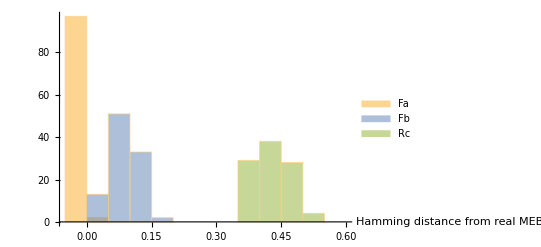

howfar_meb_subj00070_hamming.jpg

```mathematica
graph=Histogram[{hammingFAsSubj00070,hammingFBsSubj00070,hammingRCsSubj00070},bins[0.05,0.6],ChartLegends->{"Fa","Fb","Rc"},AxesLabel->{"Hamming distance from real MEB"}]
Export["howfar_meb_subj00070_hamming.jpg",graph,Path->pathBase]
```

Comment: As can be expected, the distance between the MEB code of the anchor FA face and the other FA faces are almost all 0. However, the FBs peak in the range 0.05-0.1. Thus, they are close but not exactly 0. This might suggest that further training might do the job.

More disturbing, however, is the separation between the FB’s and the RC’s. As we can see, the RC’s are all “very far away” (in this context) suggesting that the MEB codes do not respond to the pose variation. 

Question to ask: Is this because of lack of enough training or is our last layer (or the fact that we are training only on frontal images) fundamentally emphasizing the pose difference?
Idea: We can look at the Euclidean distances from an anchor FA face to all the variations to see if we get a similar distribution -- that way we can know if something is going wrong in our extra layer or if the VGG output layer is itself too sensitive to pose.

Let’s look at the same thing (distribution of the distances of the MEB codes from that of an anchor FA face to all variations of FAs, FBs, RCs), but with the Euclidean distances, i.e. before quantizing the MEB code.

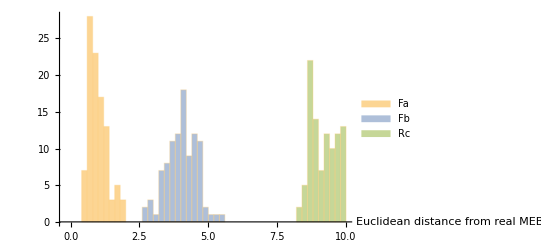

```mathematica
Histogram[{euclideanFAsSubj00070,euclideanFBsSubj00070,euclideanRCsSubj00070},bins[0.2,10],ChartLegends->{"Fa","Fb","Rc"},AxesLabel->{"Euclidean distance from real MEB code"}]
```

Comment: The Euclidean distances are bigger and more spread out (note that the bins are of bigger width and they extend further; this is because the Hamming distance was calculated as a proportion of the number of different positions out of all positions in the vector). However, the same distribution exists. Thus, it is unlikely that the quantization is causing many problems.

## Subject 00140 (Good FB but Low RC Matching Scores)

```mathematica
dataSubj00140=Import["data_howfar_meb_subject_00140.csv",Path->pathBase,HeaderLines->1];
```

Hamming distance.

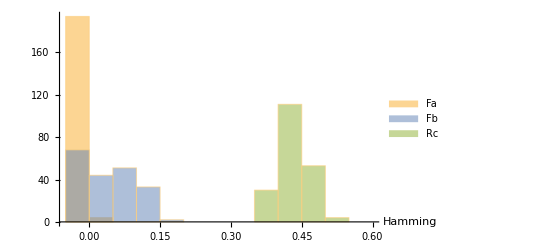

```mathematica
Histogram[{dataSubj00140[[All,4]],dataSubj00140[[All,5]],dataSubj00140[[All,6]]},bins[0.05,0.6],ChartLegends->{"Fa","Fb","Rc"},AxesLabel->{"Hamming"}]
```

Euclidean distance.

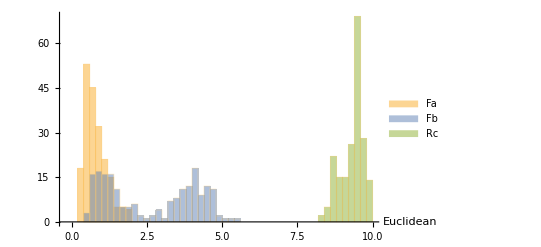

```mathematica
Histogram[{dataSubj00140[[All,1]],dataSubj00140[[All,2]],dataSubj00140[[All,3]]},bins[0.2,10],ChartLegends->{"Fa","Fb","Rc"},AxesLabel->{"Euclidean"}]
```

Comment: Perhaps it is expected that in this case, when the subject’s matching score for FB’s is high, a fair amount of the FB’s have now shifted into the 0.0 for the Hamming and overlap for the FA’s overlap.

## Subject 00468 (Almost Perfect FB but Low RC Matching Scores)

```mathematica
dataSubj00468=Import["data_howfar_meb_subject_00468.csv",Path->pathBase,HeaderLines->1];
```

Hamming distance.

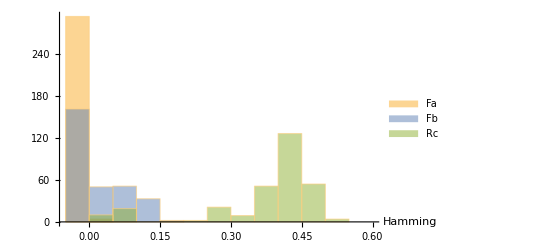

```mathematica
Histogram[{dataSubj00468[[All,4]],dataSubj00468[[All,5]],dataSubj00468[[All,6]]},bins[0.05,0.6],ChartLegends->{"Fa","Fb","Rc"},AxesLabel->{"Hamming"}]
```

Euclidean distance.

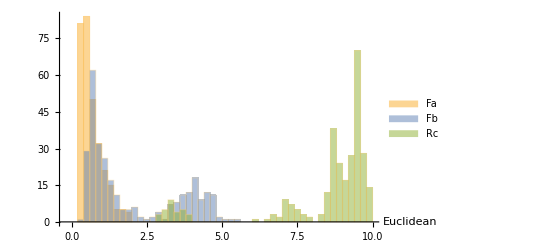

```mathematica
Histogram[{dataSubj00468[[All,1]],dataSubj00468[[All,2]],dataSubj00468[[All,3]]},bins[0.2,10],ChartLegends->{"Fa","Fb","Rc"},AxesLabel->{"Euclidean"}]
```

Comment: Again, the results aren’t unexpected. It is noticeable that the RC’s are slowly creeping into the FB territory.

## Subject 00636 (Almost Perfect FB but Middle RC Matching Scores)

```mathematica
dataSubj00636=Import["data_howfar_meb_subject_00636.csv",Path->pathBase,HeaderLines->1];
```

Hamming distance.

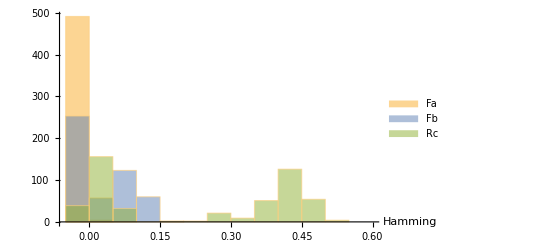

```mathematica
Histogram[{dataSubj00636[[All,4]],dataSubj00636[[All,5]],dataSubj00636[[All,6]]},bins[0.05,0.6],ChartLegends->{"Fa","Fb","Rc"},AxesLabel->{"Hamming"}]
```

## Subject 00682 (Low FB, Low RC)

```mathematica
dataSubj00682=Import["data_howfar_meb_subject_00682.csv",Path->pathBase,HeaderLines->1];
```

Hamming distance.

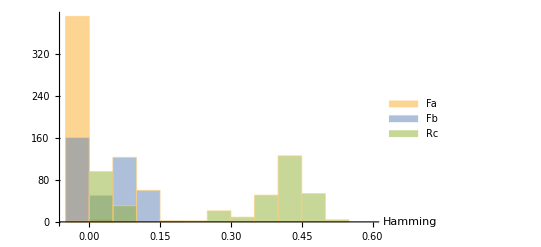

```mathematica
Histogram[{dataSubj00682[[All,4]],dataSubj00682[[All,5]],dataSubj00682[[All,6]]},bins[0.05,0.6],ChartLegends->{"Fa","Fb","Rc"},AxesLabel->{"Hamming"}]
```